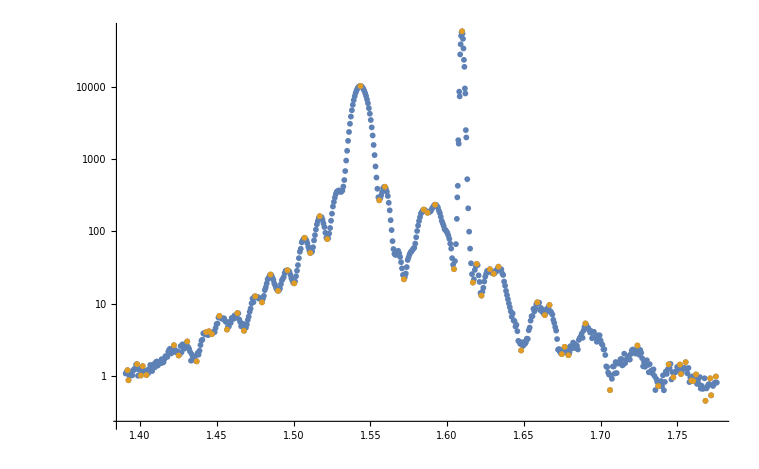

```mathematica
eRad= 2.81794*^-5; (*classical electron radius in Angstroms*)
defPolFactor=3500.0;(*polarization factor (set to 1 for now),can basically be constant might be function of theta*)
layersInSample=5;(*total number of crystal layers (i.e.materials in heterostructure)*)
wavelength = 0.709; (*x-ray wavelength from molybdenum K-alpha1*)
scaling =(* None*) "Log";
imageDimensions = {1000,1000};

(*d-spacing (Angstroms) of crystal layers from (001) direction*)
(*data taken from ICSD database:https://icsd.fiz-karlsruhe.de/search/index.xhtml*)(*Specific Sources can be found with the Collection Codes*)
(*length of cell in c-direction in database is what was taken as d-spacing*)
dSrTiO3=3.904;(*Code:23076*)
dSrRuO3 =3.964;(*Code:82977*)(*was 5.569*)
dBiFeO3 =4.072;(*Code:15299*)(*was 13.867 according to ICSD*)
dCobalt = 4.089;(*Code:44990*)
dPlatinum = 3.924;(*Code:5250*)
dSpace={dSrTiO3, dSrRuO3, dBiFeO3, dCobalt, dPlatinum};(*list of d-spacings of each crystal layer in sample*)

(*average number density of layer (atoms/cubic Angstrom)*)
(*acquired using data from ICSD*)
densSrTiO3=8.396*^-2;(*was 8.396*^-2 atoms/cubic Angstrom*)
densSrRuO3=5.0272*^-2;(*was 8.2706*^-2*)
densBiFeO3=9.8864*^-2;
densCobalt=8.9969*^-2;
densPlatinum=6.6214*^-2;
rho={densSrTiO3, densSrRuO3, densBiFeO3, densCobalt, densPlatinum};

(*list of average number densities of each layer in sample*)(*experiment uses x-rays from molybdenum K-alpha1 (wavelength~0.709 Ang,energy~17.4793 keV) http://www.med.harvard.edu/jpnm/physics/refs/xrayemis.html*)(*data taken from online NIST form factor tables http://physics.nist.gov/PhysRefData/FFast/html/form.html*)(*notable discrepancy is that data from NIST was taken for waves of energy~17.59961 keV*)(*only the real part of the atomic form factor is considered*)
affSr=36.899;(*atomic form factor of strontium e/atom*)
affTi=22.3139;
affO=8.01434;
affRu=42.9479;
affBi=80.0284;
affFe=26.4094;
affCo=27.4188;
affPt=77.1783;
affSrTiO3=affSr+affTi+3*affO;
affSrRuO3=affSr+affRu+3*affO;
affBiFeO3=affBi+affFe+3*affO;
formFactor={affSrTiO3, affSrRuO3, affBiFeO3, affCo, affPt};(*list of form factors for each layer in sample*)

(*Manipulable variable defaults*)
mDefaults = {500, 56, 157, 24, 69};
mMin = 1;
mMax = 600;
mStep = 1;

nBarDefaults = {500, 54.014, 142.465, 23.97, 68.04};
nMin = 1;
nMax = 600;
nStep = 0.1;

delDefaults = {0.2264, 2.292, 4.09, 1.0};
delMin = 0.1;
delMax = 10.0;
delStep = 0.1;

qInitDefault=1.4;
qFinDefault=1.8;

pointsPlotted = 200;
plotPointRecursion = 0;


(*******************************************************************************************************************)


(*functions for calculating specular reflectivity as outlined by Paul Miceli in Semiconductor Interfaces,Microstructures,and Devices:Properties and Applications p.87:X-ray Reflectivity from Heteroepitaxial Layers*)(*independent variable is qZ,the vertical component of the scattering vector Q.all other parameters are constants defined above or to be manipulated in simulation*)rSpec[qZ0_,polFactor0_,eRad0_,layerNum0_,rho0_,dSpace0_,formFactor0_,mL0_,nBar0_,deltaL0_]:=Module[{qZ=qZ0,polFactor=polFactor0,eRad=eRad0,layerNum=layerNum0,rho=rho0,dSpace=dSpace0,formFactor=formFactor0,mL=mL0,nBar=nBar0,deltaL=deltaL0,r},

r=Abs[polFactor*(16*Pi^2*eRad^2/qZ^2)*Norm[scatAmp[qZ,layerNum,rho,dSpace,formFactor,mL,nBar,deltaL]]^2];
(*Echo[N[r]];*)
(*Echo[N[Norm[scatAmp[qZ,layerNum,rho,dSpace,formFactor,mL,nBar,deltaL]]]];*)
r
]



(*the average scattering amplitude*)
scatAmp[qZ0_,layerNum0_,rho0_,dSpace0_,formFactor0_,mL0_,nBar0_,deltaL0_]:=
Module[{qZ=qZ0,layerNum=layerNum0,rho=rho0,dSpace=dSpace0,formFactor=formFactor0,mL=mL0,nBar=nBar0,deltaL=deltaL0,vL,i,aSub,aL,sum},
(*Echo[qZ];*)
vL=Table[calcV[qZ,j,dSpace[[j]],mL[[j]],nBar[[j]]],{j,layerNum}];
i=1;
aSub=rho[[i]]*dSpace[[i]]*formFactor[[i]]*vL[[i]]/(1-Exp[-I*qZ*dSpace[[i]]]);
sum=aSub;

i=2;
While[i<=layerNum,
aL=rho[[i]]*dSpace[[i]]*formFactor[[i]]*(vL[[i]]-1)/(1-Exp[-I*qZ*dSpace[[i]]]);
sum+=Product[vL[[j]],{j,i-1}]*Exp[I*qZ*Sum[deltaL[[j]],{j,i-1}]]*aL;
i++;
(*Echo[i];*)
];
(*Echo[sum];*)

sum
]



(*calculate V,essentially the roughness*)
calcV[qZ0_,i0_,d0_,m0_,n0_]:=
Module[{qZ=qZ0, i=i0, d=d0, m=m0, n=n0},
	If[i==1,
	Exp[-2*n*(1-(n/m))*Sin[0.5*qZ*d]^2],

	((n/m)*Exp[I*qZ*d]+(1-(n/m)))^m
]
]

(*getResiduals[]*)



thetaToQ[twoTheta_]:=(4*Pi*Sin[twoTheta/2  Degree] / wavelength)


(*******************************************************************************************************************)


(*Set up plots of BFO Reflectivity data taken by Jesse Kremenak*)

Needs["ErrorBarPlots`"]; (*load up Error Bar Plots package*)
(*  b986-1-Bragg001-2theta  *)
data986Bragg001Theta = Import["Z:\\xrd_mathematica\\BFO_Reflectivity_data\\b986-1-Bragg001-final.dat", "Table"] ;(*import data from file*)
For[i=1,i≤Length[data986Bragg001Theta],i++,
	data986Bragg001Theta[[i,1]]=thetaToQ[data986Bragg001Theta[[i,1]]];
];
plotReadyData = Table[{data986Bragg001Theta[[i,{1,2}]], ErrorBarPlots`ErrorBar[data986Bragg001Theta[[i,3]]]}, {i,Length[data986Bragg001Theta]}];
plot986Bragg001Theta = ErrorListPlot[plotReadyData, ScalingFunctions->scaling, ImageSize->imageDimensions, PlotLegends->{"b986 (001) Q"}];

(*  b987-1-Bragg001-2theta  *)
data987Bragg001Theta = Import["Z:\\xrd_mathematica\\BFO_Reflectivity_data\\b987-1-Bragg001-final.dat", "Table"] ;(*import data from file*)
For[i=1,i≤Length[data987Bragg001Theta],i++,
	data987Bragg001Theta[[i,1]]=thetaToQ[data987Bragg001Theta[[i,1]]];
];
plotReadyData2 = Table[{data987Bragg001Theta[[i,{1,2}]], ErrorBarPlots`ErrorBar[data987Bragg001Theta[[i,3]]]}, {i,Length[data987Bragg001Theta]}];
plot987Bragg001Theta = ErrorListPlot[plotReadyData2, ScalingFunctions->scaling, ImageSize->imageDimensions,PlotStyle->Red, PlotLegends->{"b987 (001) θ"}];

(*  b987-1-Bragg001-q  *)
data987Bragg001Q = Import["Z:\\xrd_mathematica\\BFO_Reflectivity_data\\b987-1-Bragg001-final-q.txt", "Table"] ;(*import data from file*)
plotReadyData3 = Table[{data987Bragg001Q[[i,{1,2}]], ErrorBarPlots`ErrorBar[data987Bragg001Q[[i,3]]]}, {i,Length[data987Bragg001Q]}];
plot987Bragg001Q = ErrorListPlot[plotReadyData, ScalingFunctions->scaling, ImageSize->imageDimensions, PlotLegends->{"b987 (001) Q"}];

fitPeakDataOnly=True;
allFitData=Drop[data987Bragg001Theta, None, {3}];
sigmaExtrema=2;
peakData=FindPeaks[allFitData[[All,2]],sigmaExtrema];
valleyData=# {1,-1}&/@FindPeaks[-allFitData[[All,2]],sigmaExtrema];
extremaData=Join[peakData,valleyData];
For[i=1,i≤Length[extremaData],i++,
extremaData[[i,1]]=allFitData[[extremaData[[i,1]],1]];
];
ListPlot[{allFitData,extremaData},ScalingFunctions->"Log"]

dataToFit={};
If[fitPeakDataOnly,
dataToFit=extremaData;
,
dataToFit=allFitData;
];

(*******************************************************************************************************************)

computeResiduals[nParams0_,mParams0_,delParams0_,rhoParams0_,latticeParams0_,polFactor0_,dataStart0_,dataEnd0_]:=
Module[{nParams=nParams0,mParams=mParams0,delParams=delParams0,rhoParams=rhoParams0,latticeParams=latticeParams0,polFactor=polFactor0,dataStart=dataStart0,dataEnd=dataEnd0,layerNum=3,s=0},
	For[i=dataStart,i<dataEnd,i++,
		s +=(Log[dataToFit[[i,2]]]-Log[rSpec[dataToFit[[i,1]],polFactor,eRad,layerNum,rhoParams,latticeParams,formFactor,mParams,nParams,delParams]])^2;
];
s
]

(*perturbState[nPerturbations0_,mPerturbations0_,delPerturbations0_,mMaxPert0_,nMaxPert0_,delMaxPert0_]:=
Module[{nPerturbations=nPerturbations0,mPerturbations=mPerturbations0,delPerturbations=delPerturbations0,mMaxPert=mMaxPert0,nMaxPert=nMaxPert0,delMaxPert=delMaxPert0},
For[i=1,i≤Length[nPerturbations],i++,

];
*)
```

```mathematica
numRandStates=10;
numSteps=10;

mSampleRange=10;
nSampleRange=6;
delSampleRange=3;
dSpaceSampleRange=0.01;
densSampleRange=0.1*^-2;
polFactorSampleRange=500;

mMaxStep=1;
nMaxStep=1;
delMaxStep=0.3;
dSpaceMaxStep=0.01;
densMaxStep=0.1*^-2;
polFactorMaxStep=100;

mInit={0,5,5,0};

startDatum=1;
endDatum=Length[dataToFit];

iRes=1;
iSTOn=2;
iSTOm=3;
iSTOdel=4;
iSTOdSpace=5;
iSTOdens=6;
iSROn=7;
iSROm=8;
iSROdel=9;
iSROdSpace=10;
iSROdens=11;
iBFOn=12;
iBFOm=13;
iBFOdel=14;
iBFOdSpace=15;
iBFOdens=16;
iCOn=17;
iCOm=18;
iCOdel=19;
iCodSpace=20;
iCOdens=21;
iPtdens=22;
iPtdSpace=23;
ipolFactor=24;

realPerturb[halfRange_]:=Abs[RandomReal[{-halfRange,halfRange}]];
intPerturb[halfRange_]:=Abs[RandomInteger[{-halfRange,halfRange}]];
genPerturb={realPerturb,intPerturb};
(*First value indicates the index of characteristic to be perturbed in perturbedState. Second value indicates type of perturbation (1 for real values, 2 for integer values. Third value indicates range of perturbation*)
traitsToPerturb={{iSTOdel,1,delMaxStep},{iSROn,1,nMaxStep},{iSROm,2,mMaxStep},{iSROdel,1,delMaxStep},{iSROdens,1,densMaxStep},{iSROdSpace,1,dSpaceMaxStep},{iBFOn,1,nMaxStep},{iBFOm,2,mMaxStep},{iBFOdel,1,delMaxStep},{iBFOdens,1,densMaxStep},{iBFOdSpace,1,dSpaceMaxStep},{iBFOdens,1,densMaxStep},{ipolFactor,2,polFactorMaxStep}};

perturbation=traitsToPerturb;

unperturbedStartingState=(*{332.3961079631692,500,500,0.02166781942475532,3.904,0.08396,51.9665635248197,53,1.7333696566354275,3.9929932082688344,0.054579364344248635,140.3090383181321,178,3.576833726592395,4.072,0.10497485962095837,23.97,35,1.,4.089,0.089969,0.066214,3.924,3407.};*){910.6987523573418,500,500,1.1980063519456072,3.904,0.08396,54.23358554139635,66,1.8771515728306518,3.964,0.050272,144.13973555643094,158,5.138193668233221,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.};
perturbStart=False;
```

```mathematica
(*Initialize Current States*)
currentStates=Table[0,{k,numRandStates},{j,ipolFactor}];
If[perturbStart,
For[k=1,k<=numRandStates,k++,
currentStates[[k,iSTOn]]=nBarDefaults[[1]];
currentStates[[k,iSTOm]]=mDefaults[[1]];
currentStates[[k,iSTOdel]]=Abs[delDefaults[[1]]+RandomReal[{-delSampleRange/2,delSampleRange/2}]];
currentStates[[k,iSROn]]=nBarDefaults[[2]]+RandomReal[{-nSampleRange/2,nSampleRange/2}];
currentStates[[k,iSROm]]=Ceiling[currentStates[[k,iSROn]]+mInit[[2]]]+RandomInteger[mSampleRange];
currentStates[[k,iSROdel]]=Abs[delDefaults[[2]]+RandomReal[{-delSampleRange/2,delSampleRange/2}]];
currentStates[[k,iBFOn]]=nBarDefaults[[3]]+RandomReal[{-nSampleRange/2,nSampleRange/2}];
currentStates[[k,iBFOm]]=Ceiling[currentStates[[k,iBFOn]]+mInit[[3]]]+RandomInteger[mSampleRange];
currentStates[[k,iBFOdel]]=Abs[delDefaults[[3]]+RandomReal[{-delSampleRange/2,delSampleRange/2}]];
currentStates[[k,iCOm]]=mDefaults[[4]]+RandomInteger[mSampleRange];
currentStates[[k,iCOn]]=nBarDefaults[[4]];
currentStates[[k,iCOdel]]=delDefaults[[4]];
currentStates[[k,iSTOdens]]=rho[[1]](*+RandomReal[{-dSpaceSampleRange,dSpaceSampleRange}]*);
currentStates[[k,iSROdens]]=rho[[2]];
currentStates[[k,iBFOdens]]=rho[[3]];
currentStates[[k,iCOdens]]=rho[[4]];
currentStates[[k,iPtdens]]=rho[[5]];
currentStates[[k,iSTOdSpace]]=dSpace[[1]](*+RandomReal[{-dSpaceSampleRange,dSpaceSampleRange}]*);
currentStates[[k,iSROdSpace]]=dSpace[[2]];
currentStates[[k,iBFOdSpace]]=dSpace[[3]];
currentStates[[k,iCodSpace]]=dSpace[[4]];
currentStates[[k,iPtdSpace]]=dSpace[[5]];
currentStates[[k,ipolFactor]]=defPolFactor+RandomInteger[{-polFactorSampleRange,polFactorSampleRange}];
currentStates[[k,iRes]]=computeResiduals[{currentStates[[k,iSTOn]],currentStates[[k,iSROn]],currentStates[[k,iBFOn]],currentStates[[k,iCOn]]},
								{currentStates[[k,iSTOm]],currentStates[[k,iSROm]],currentStates[[k,iBFOm]],currentStates[[k,iCOm]]},
								{currentStates[[k,iSTOdel]],currentStates[[k,iSROdel]],currentStates[[k,iBFOdel]],currentStates[[k,iCOdel]]},
								{currentStates[[k,iSTOdens]],currentStates[[k,iSROdens]],currentStates[[k,iBFOdens]],currentStates[[k,iCOdens]]},
								{currentStates[[k,iSTOdSpace]],currentStates[[k,iSROdSpace]],currentStates[[k,iBFOdSpace]],currentStates[[k,iCodSpace]],currentStates[[k,iPtdSpace]]},
								currentStates[[k,ipolFactor]],startDatum,endDatum];
];
,
For[k=1,k<=numRandStates,k++,
currentStates[[k]]=unperturbedStartingState;
];
];
currentStates=SortBy[currentStates,First];
For[k=1,k<=numRandStates,k++,
	Echo[currentStates[[k]]];
];

(*currentStates={{549.9022319058445,498,498,3.744962804387865,42.559785159231176,44,1.1182025947283316,143.7912931053952,155,4.1,23.97,24,1.},
{583.0635359965215,498,498,6.417213670023052,49.872033185591825,64,1.1748486680938155,140.72788281812436,148,1.1870683215562807,23.97,24,1.},
{588.3894551190804,498,498,2.675209498195954,50.10255268540891,63,1.1008007124015675,138.92912118238576,156,1.1660849311173138,23.97,24,1.}}*)
```

{910.699,500,500,1.19801,3.904,0.08396,54.2336,66,1.87715,3.964,0.050272,144.14,158,5.13819,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.}

{910.699,500,500,1.19801,3.904,0.08396,54.2336,66,1.87715,3.964,0.050272,144.14,158,5.13819,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.}

{910.699,500,500,1.19801,3.904,0.08396,54.2336,66,1.87715,3.964,0.050272,144.14,158,5.13819,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.}

«7 more identical outputs»

```mathematica
(*Begin the Markov Chain*)
beginTime=AbsoluteTime[];
For[n=1,n≤numSteps,n++,
For[k=1,k≤numRandStates,k++,
perturbedState=currentStates[[k]];
perturbedState[[iSTOdel]]=Abs[perturbedState[[iSTOdel]]+RandomReal[{-delMaxStep,delMaxStep}]];
perturbedState[[iSROn]]=perturbedState[[iSROn]]+RandomReal[{-nMaxStep,nMaxStep}];
perturbedState[[iSROm]]=perturbedState[[iSROm]]+RandomInteger[{-mMaxStep,mMaxStep}];
perturbedState[[iSROdel]]=Abs[perturbedState[[iSROdel]]+RandomReal[{-delMaxStep,delMaxStep}]];
perturbedState[[iBFOn]]=perturbedState[[iBFOn]]+RandomReal[{-nMaxStep,nMaxStep}];
perturbedState[[iBFOm]]=perturbedState[[iBFOm]]+RandomInteger[{-mMaxStep,mMaxStep}];
perturbedState[[iBFOdel]]=Abs[perturbedState[[iBFOdel]]+RandomReal[{-delMaxStep,delMaxStep}]];
perturbedState[[iCOm]]=perturbedState[[iCOm]]+RandomInteger[{-mMaxStep,mMaxStep}];
(*perturbedState[[iSTOdSpace]]=perturbedState[[iSTOdSpace]]+RandomReal[{-dSpaceMaxStep,dSpaceMaxStep}];*)
perturbedState[[iSROdSpace]]=perturbedState[[iSROdSpace]]+RandomReal[{-dSpaceMaxStep,dSpaceMaxStep}];
perturbedState[[ipolFactor]]=perturbedState[[ipolFactor]]+RandomInteger[{-polFactorMaxStep,polFactorMaxStep}];
perturbedState[[iSROdens]]=Abs[perturbedState[[iSROdens]]+RandomReal[{-densMaxStep,densMaxStep}]];
perturbedState[[iBFOdens]]=Abs[perturbedState[[iBFOdens]]+RandomReal[{-densMaxStep,densMaxStep}]];

perturbedState[[iRes]]=computeResiduals[{perturbedState[[iSTOn]],perturbedState[[iSROn]],perturbedState[[iBFOn]],perturbedState[[iCOn]]},
								{perturbedState[[iSTOm]],perturbedState[[iSROm]],perturbedState[[iBFOm]],perturbedState[[iCOm]]},
								{perturbedState[[iSTOdel]],perturbedState[[iSROdel]],perturbedState[[iBFOdel]],perturbedState[[iCOdel]]},
								{perturbedState[[iSTOdens]],perturbedState[[iSROdens]],perturbedState[[iBFOdens]],perturbedState[[iCOdens]]},
								{perturbedState[[iSTOdSpace]],perturbedState[[iSROdSpace]],perturbedState[[iBFOdSpace]],perturbedState[[iCodSpace]],perturbedState[[iPtdSpace]]},
								perturbedState[[ipolFactor]],startDatum,endDatum];

acceptanceProb=Exp[currentStates[[k,iRes]]-perturbedState[[iRes]]];
strictCostlyAcceptanceRatio=0.5;(*Probability of accepting any perturbation which results in a higher residual sum; meant to prevent from accepting many tiny, bad perturbations*)
acceptanceRatio=RandomReal[];(*Additional acceptance ratio. Randomness ensures less costly perturbations are more likely to occur*)
If[(acceptanceProb>acceptanceRatio)&&(perturbedState[[iSROm]]>perturbedState[[iSROn]])&&(perturbedState[[iBFOm]]>perturbedState[[iBFOn]]),
If[acceptanceProb<1,
If[RandomReal[]>strictCostlyAcceptanceRatio,
currentStates[[k]]=perturbedState;
];,
currentStates[[k]]=perturbedState;
];
];

];
];

endTime=AbsoluteTime[];
Echo[endTime-beginTime,"Time Elapsed: "];

(*Print Results*)
currentStates=SortBy[currentStates,First];
For[k=1,k<=numRandStates,k++,
	Echo[currentStates[[k]]];
];
(*Do[Print[currentStates[[k]]],{k,numRandStates}];*)
```

```mathematica
(******************************************************************************************************************************************)
(* Monte Carlo with single perturbation at a time *)
(******************************************************************************************************************************************)
beginTime=AbsoluteTime[];
(*Begin the Markov Chain*)
For[n=1,n≤numSteps,n++,
For[k=1,k≤numRandStates,k++,
For[i=1,i≤Length[traitsToPerturb],i++,
j=traitsToPerturb[[i,1]];
perturbedState=currentStates[[k]];
perturbedState[[j]]=perturbedState[[j]]+genPerturb[[traitsToPerturb[[i,2]]]][traitsToPerturb[[i,3]]];
perturbedState[[iRes]]=computeResiduals[{perturbedState[[iSTOn]],perturbedState[[iSROn]],perturbedState[[iBFOn]],perturbedState[[iCOn]]},
								{perturbedState[[iSTOm]],perturbedState[[iSROm]],perturbedState[[iBFOm]],perturbedState[[iCOm]]},
								{perturbedState[[iSTOdel]],perturbedState[[iSROdel]],perturbedState[[iBFOdel]],perturbedState[[iCOdel]]},
								{perturbedState[[iSTOdens]],perturbedState[[iSROdens]],perturbedState[[iBFOdens]],perturbedState[[iCOdens]]},
								{perturbedState[[iSTOdSpace]],perturbedState[[iSROdSpace]],perturbedState[[iBFOdSpace]],perturbedState[[iCodSpace]],perturbedState[[iPtdSpace]]},
								perturbedState[[ipolFactor]],startDatum,endDatum];

acceptanceProb=Exp[currentStates[[k,iRes]]-perturbedState[[iRes]]];
strictCostlyAcceptanceRatio=0.5;(*Probability of accepting any perturbation which results in a higher residual sum; meant to prevent from accepting many tiny, bad perturbations*)
acceptanceRatio=RandomReal[];(*Additional acceptance ratio. Randomness ensures less costly perturbations are more likely to occur*)
If[(acceptanceProb>acceptanceRatio)&&(perturbedState[[iSROm]]>perturbedState[[iSROn]])&&(perturbedState[[iBFOm]]>perturbedState[[iBFOn]]),
If[acceptanceProb<1,
If[RandomReal[]>strictCostlyAcceptanceRatio,
currentStates[[k]]=perturbedState;
];,
currentStates[[k]]=perturbedState;
];
];
];
];
];

endTime=AbsoluteTime[];
Echo[endTime-beginTime,"Time Elapsed: "];

(*Print Results*)
currentStates=SortBy[currentStates,First];
For[k=1,k<=numRandStates,k++,
	Echo[currentStates[[k]]];
];
(*Do[Print[currentStates[[k]]],{k,numRandStates}];*)
```

Time Elapsed:  9.587

{812.947,500,500,1.5829,3.904,0.08396,54.2336,66,1.87715,3.964,0.050272,144.14,158,5.13819,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.}

{813.01,500,500,1.57513,3.904,0.08396,54.2336,66,1.87715,3.964,0.050272,144.14,158,5.13819,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.}

{813.121,500,500,1.59097,3.904,0.08396,54.2336,66,1.87715,3.964,0.050272,144.14,158,5.13819,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.}

{813.361,500,500,1.59622,3.904,0.08396,54.2336,66,1.87715,3.964,0.050272,144.14,158,5.13819,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.}

{814.175,500,500,1.60711,3.904,0.08396,54.2336,66,1.87715,3.964,0.050272,144.14,158,5.13819,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.}

{814.433,500,500,1.554,3.904,0.08396,54.2336,66,1.87715,3.964,0.050272,144.14,158,5.13819,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.}

{818.728,500,500,1.63649,3.904,0.08396,54.2336,66,1.87715,3.964,0.050272,144.14,158,5.13819,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.}

{820.791,500,500,1.64474,3.904,0.08396,54.2336,66,1.87715,3.964,0.050272,144.14,158,5.13819,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.}

{823.751,500,500,1.65417,3.904,0.08396,54.2336,66,1.87715,3.964,0.050272,144.14,158,5.13819,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.}

{844.53,500,500,1.7718,3.904,0.08396,54.2336,66,1.87715,3.964,0.050272,144.14,158,5.13819,4.072,0.098864,23.97,29,1.,4.089,0.089969,0.066214,3.924,3567.}

```mathematica
Export["MCfits_only_BFO.dat",currentStates];
```